# Pêndulo livre sem controlo, teste numérico usando stormer verlet e Runge-kutta

```mathematica
ClearAll["Global`*"]
ClearAll[Subscript]
ClearAll[Derivative]
```

## Contas teóricas

### Lagrangeano do Pêndulo esférico

```mathematica
L=1/2(θ'[t]^2+Sin[θ[t]]^2  ϕ'[t]^2)-Subscript[ω, 0]^2 Cos[θ[t]]
```

-Cos[θ[t]] ω_0^2+1/2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

### Equação de movimento

```mathematica
D[D[L,θ'[t]],t]-D[L,θ[t]]
```

-Sin[θ[t]] ω_0^2-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]

### Condição de conservação

```mathematica
A={ϕ'[t]->C/Sin[θ[t]]^2}
```

{ϕ'[t]→C Csc[θ[t]]^2}

### Hamiltoniano

```mathematica
H=θ'[t] D[L,θ'[t]]+ϕ'[t] D[L,ϕ'[t]]-L/.A/.θ'[t]->Subscript[p, θ][t]//FullSimplify
```

1/2 (C^2 Csc[θ[t]]^2+2 Cos[θ[t]] ω_0^2+p_θ[t]^2)

### Parametros Físicos

```mathematica
g=1;
l=1;
paramFis={Subscript[ω, 0]^2->g/l,C->1}
```

{ω_0^2→1,C→1}

## Integração numérica

```mathematica
Subscript[H, NUM]=H/.paramFis
```

1/2 (2 Cos[θ[t]]+Csc[θ[t]]^2+p_θ[t]^2)

### Stormer-Verlet

#### Equações do movimento

```mathematica
D[H,Subscript[p, θ][t]]//FullSimplify
D[H,θ[t]]//FullSimplify
```

p_θ[t]

-Sin[θ[t]] (C^2 Cot[θ[t]] Csc[θ[t]]^3+ω_0^2)

#### Parametros numéricos

```mathematica
Δt=0.001;
nMAX=6200;
```

### Integração para θ e p_θ usando Stormer-Verlet e Euler para ϕ

```mathematica
Subscript[ϕ, SV]'[t_]:=C/Sin[Subscript[θ, SV][t]]^2/.paramFis
```

```mathematica
For[Subscript[θ, SV][0]={(2π)/3};Subscript[p, SV][0]={0};n=0;Subscript[ϕ, SV][0]={π/2},n<nMAX,n++,

(*H1=(∂H)/(∂q)(Subscript[p, n+1/2],Subscript[θ, n])*)
H1=D[Subscript[H, NUM],θ[t]]/.{Subscript[p, θ][t]->Subscript[p, SV][n+1/2],θ[t]->Subscript[θ, SV][n]};
subs=Solve[Subscript[p, SV][n+1/2]==Subscript[p, SV][n]-Δt/2 H1,Subscript[p, SV][n+1/2]];
Subscript[p, SV][n+1/2]=Subscript[p, SV][n+1/2]/.subs;


(*H2=(∂H)/(∂p)(Subscript[p, n+1/2],Subscript[θ, n]);H3=(∂H)/(∂p)(Subscript[p, n+1/2],Subscript[θ, n+1])*)
H2= D[Subscript[H, NUM],Subscript[p, θ][t]]/.{Subscript[p, θ][t]->Subscript[p, SV][n+1/2],θ[t]->Subscript[θ, SV][n]};
H3=D[Subscript[H, NUM],Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, SV][n+1/2]/.Subscript[θ, SV][n]->Subscript[θ, SV][n+1];
subs2=Solve[Subscript[θ, SV][n+1]==Subscript[θ, SV][n]+Δt/2(H1 + H2),Subscript[θ, SV][n+1]];
Subscript[θ, SV][n+1]=Subscript[θ, SV][n+1]/.subs2;

(*Método de Euler para ϕ*)
Subscript[ϕ, SV][n+1]=Subscript[ϕ, SV]'[n] Δt + Subscript[ϕ, SV][n];
 
(*Condições Fronteira*)
If[Subscript[θ, SV][n+1]>π,Subscript[ϕ, SV][n+1]=Subscript[ϕ, SV][n+1]+π;Subscript[θ, SV][n+1]=2π-Subscript[θ, SV][n+1];Subscript[p, SV][n+1/2]=-Subscript[p, SV][n+1/2]];
If[Subscript[θ, SV][n+1]<0,Subscript[ϕ, SV][n+1]=Subscript[ϕ, SV][n+1]+π;Subscript[θ, SV][n+1]=-Subscript[θ, SV][n+1];Subscript[p, SV][n+1/2]=-Subscript[p, SV][n+1/2]];

(*H4=(∂H)/(∂q)(Subscript[p, n+1/2],Subscript[θ, n+1])*)
	H4=D[Subscript[H, NUM],θ[t]]/.θ[t]->Subscript[θ, SV][n+1]/.Subscript[p, SV][n]->Subscript[p, SV][n+1/2];
	Subscript[p, SV][n+1]=Subscript[p, SV][n+1/2]-Δt/2 H4]
```

## Integração de θ, Runge-Kutta 4.aa ordem e ϕ por Euler

```mathematica
Subscript[ϕ, RK4]'[t_]:=C/Sin[Subscript[θ, RK4][t]]^2/.paramFis
```

```mathematica
For[Subscript[θ, RK4][0]={(2π)/3};Subscript[p, RK4][0]={0};Subscript[ϕ, RK4][0]={0};i=0,i<nMAX,i++,
(*θ̇=(∂H)/(∂p)*)
K1=D[Subscript[H, NUM],Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, RK4][i];
K2=D[Subscript[H, NUM],Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, RK4][i]+Δt/2 K1;
K3=D[Subscript[H, NUM],Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, RK4][i]+Δt/2 K2;
K4=D[Subscript[H, NUM],Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, RK4][i]+Δt K3;
(*OverDot[Subscript[p, θ]]=-(∂H)/(∂q)*)
G1=-D[Subscript[H, NUM],θ[t]]/.θ[t]->Subscript[θ, RK4][i];
G2=-D[Subscript[H, NUM],θ[t]]/.θ[t]->Subscript[θ, RK4][i]+Δt/2 G1;
G3=-D[Subscript[H, NUM],θ[t]]/.θ[t]->Subscript[θ, RK4][i]+Δt/2 G2;
G4=-D[Subscript[H, NUM],θ[t]]/.θ[t]->Subscript[θ, RK4][i]+Δt G3;

(*Próxima iteração*)
Subscript[θ, RK4][i+1]=Subscript[θ, RK4][i]+Δt/6(K1+K2+K3+K4);
Subscript[p, RK4][i+1]=Subscript[p, RK4][i]+Δt/6(G1+G2+G3+G4);
Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4]'[i] Δt + Subscript[ϕ, RK4][i];


(*Condições Fronteira*)
If[Subscript[θ, RK4][i+1]>π,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π;Subscript[θ, RK4][i+1]=2π-Subscript[θ, RK4][i+1];Subscript[p, RK4][i+1]=-Subscript[p, RK4][i+1]];

If[Subscript[θ, RK4][i+1]<0,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π ;  Subscript[θ, RK4][i+1]=-Subscript[θ, RK4][i+1] ; Subscript[p, RK4][i+1]=-Subscript[p, RK4][i+1]]]
```

## Resulados

### Stormer-Verlet

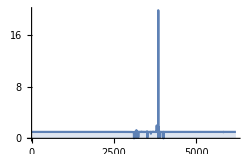

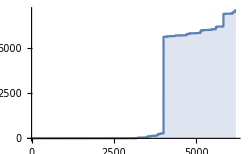

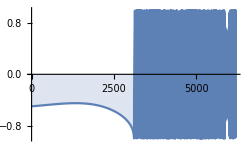

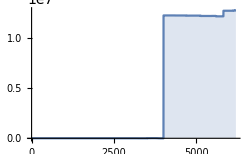

```mathematica
Subscript[H, Subscript[PLOT, SV]][n_]:=Subscript[H, NUM]/.{θ[t]->Subscript[θ, SV][n],Subscript[p, θ][t]->Subscript[p, SV][n]}
DiscretePlot[(Subscript[H, Subscript[PLOT, SV]][n])/(Subscript[H, Subscript[PLOT, SV]][n+1]),{n,0,nMAX},PlotRange->All]
DiscretePlot[Subscript[ϕ, SV][n],{n,0,nMAX},PlotRange->All]
DiscretePlot[Cos[Subscript[θ, SV][n]],{n,0,nMAX},PlotRange->All](*Está mal*)
DiscretePlot[Subscript[p, SV][n],{n,0,nMAX},PlotRange->All]
```

### RK4

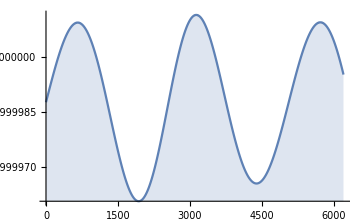

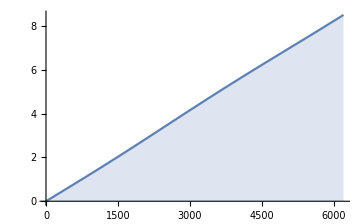

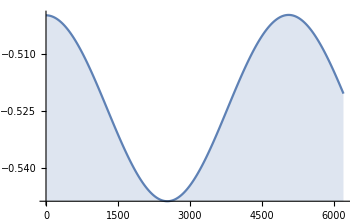

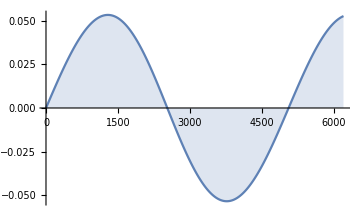

```mathematica
Subscript[H, Subscript[PLOT, RK4]][n_]:=Subscript[H, NUM]/.{θ[t]->Subscript[θ, RK4][n],Subscript[p, θ][t]->Subscript[p, RK4][n]}
DiscretePlot[(Subscript[H, Subscript[PLOT, RK4]][n])/(Subscript[H, Subscript[PLOT, RK4]][n+1]),{n,0,nMAX},PlotRange->All]
DiscretePlot[Subscript[ϕ, RK4][n],{n,0,nMAX},PlotRange->All]
DiscretePlot[Cos[Subscript[θ, RK4][n]],{n,0,nMAX},PlotRange->All]
DiscretePlot[Subscript[p, RK4][n],{n,0,nMAX},PlotRange->All]
```